```mathematica
u=0.001;
s=NDSolve[
{
b11r'[l]==-(b12r[l])^2-3/16 b12r[l]^2+4 u12r[l]^2+3/4 u12s[l]^2,
b11s'[l]==-2b12r[l]b12s[l]-1/2 b12s[l]^2-b11s[l]^2-8u12r[l]u12s[l]-2 u12s[l]^2,
b12r'[l]== -2b11r[l]b12r[l]-3/8 b11s[l]b12s[l]+2b12r[l]f12r[l]+3/8 b12s[l]f12s[l]+16u12r[l]u11r[l],
b12s'[l]==-2b11r[l]b12s[l]-2b12r[l]b11s[l]-b12s[l]b11s[l]+16u11r[l]u12s[l]+2f12r[l]b12s[l]+2b12r[l]f12s[l]-b12s[l]f12s[l],
f12r'[l]==b12r[l]^2+3/16 b12s[l]^2+16 u11r[l]^2+4 u12r[l]^2+3/4 u12s[l]^2,
f12s'[l]==2b12r[l]b12s[l]-1/2 b12s[l]^2-f12s[l]^2+8u12r[l]u12s[l]-2 u12s[l]^2,
u11r'[l]==2b12r[l]u12r[l]+4f12r[l]u11r[l]+3/8 b12s[l]u12s[l],
u12r'[l]==2b11r[l]u12r[l]-3/8 b11s[l]u12s[l]+4b12r[l]u11r[l]+2f12r[l]u12r[l]+3/8 f12s[l]u12s[l],
u12s'[l]==-2b11s[l]u12r[l]+2b11r[l]u12s[l]-b11s[l]u12s[l]+4b12s[l]u11r[l]+2f12s[l]u12r[l]+2f12r[l]u12s[l]-f12s[l]u12s[l],
b11r[0]==u,
b11s[0]==u,
b12r[0]==u,
b12s[0]==u,
f12r[0]==u,
f12s[0]==u,
u11r[0]==u,
u12r[0]==u,
u12s[0]==u

}

,{b11r,b11s,b12r,b12s,f12r,f12s,u11r,u12r,u12s},{l,0,100}];
```

NDSolve::ndsz: At l == 97.7358, step size is effectively zero; singularity or stiff system suspected.

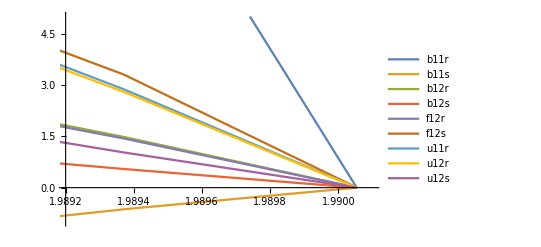

```mathematica
Plot[Evaluate[{1/b11r[10^l],1/b11s[10^l],1/b12r[10^l],1/b12s[10^l],1/f12r[10^l],1/f12s[10^l],1/u11r[10^l],1/u12r[10^l],1/u12s[10^l]}/.s],{l,0,Log[10,97.73578]},PlotRange->{{1.9892,1.9901},{-1,5}},PlotLegends->{b11r,b11s,b12r,b12s,f12r,f12s,u11r,u12r,u12s},LabelStyle->Medium]
```

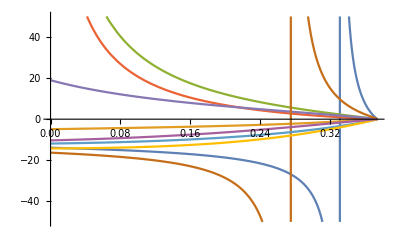

```mathematica
Plot[Evaluate[{1/b11r[10^l],1/b11s[10^l],1/b12r[10^l],1/b12s[10^l],1/f12r[10^l],1/f12s[10^l],1/u11r[10^l],1/u12r[10^l],1/u12s[10^l]}/.s],{l,0,Log[10,2.3657]},PlotRange->{{0,Log[10,2.3657]},{-50,50}}]
```

```mathematica
b12r = g
```

```mathematica
σ[[1]]
```

{{0,1},{1,0}}

```mathematica
σ={({{0, 1}, {1, 0}}),({{0, -ⅈ}, {ⅈ, 0}}),({{1, 0}, {0, -1}})};
ϵ=Normal[LeviCivitaTensor[2]];
```

```mathematica
(*C[L/R][1/2][up/down]*)
```

```mathematica
c=Array[ToExpression["c"<>ToString[#1]<>ToString[#2]<>ToString[#3]]&,{2,2,2}];
cd=Array[ToExpression["cd"<>ToString[#1]<>ToString[#2]<>ToString[#3]]&,{2,2,2}];
```

```mathematica
Js[L_,i_,j_]:=Sum[cd[[L]][[i]][[a]]**c[[L]][[j]][[a]],{a,1,2}]
Jv[L_,i_,j_]:=Table[1/2 Sum[σ[[k]][[a]][[b]]cd[[L]][[i]][[a]]**c[[L]][[j]][[b]],{a,1,2},{b,1,2}],{k,1,3}]
Is[L_,i_,j_]:=Sum[ϵ[[a]][[b]]c[[L]][[i]][[a]]**c[[L]][[j]][[b]],{a,1,2},{b,1,2}]
Iv[L_,i_,j_]:=1/2 Table[Sum[σ[[k]][[a]][[b]]ϵ[[a]][[b]]c[[L]][[i]][[a]]**c[[L]][[j]][[b]],{a,1,2},{b,1,2}],{k,1,3}]
Isd[L_,i_,j_]:=Sum[ϵ[[a]][[b]]cd[[L]][[j]][[b]]**cd[[L]][[i]][[a]],{a,1,2},{b,1,2}]
Ivd[L_,i_,j_]:=1/2 Table[Sum[σ[[k]][[a]][[b]]ϵ[[a]][[b]]cd[[L]][[j]][[b]]**cd[[L]][[i]][[a]],{a,1,2},{b,1,2}],{k,1,3}]
```

```mathematica
rule=Flatten[Table[{ToExpression["c"<>ToString[r]<>ToString[i]<>ToString[o]]->ToExpression["c"<>ToString[r]<>ToString[(i-1)*2+o]],ToExpression["cd"<>ToString[r]<>ToString[i]<>ToString[o]]->ToExpression["cd"<>ToString[r]<>ToString[(i-1)*2+o]]},{r,1,2},{i,1,2},{o,1,2}]]
```

{c111→c11,cd111→cd11,c112→c12,cd112→cd12,c121→c13,cd121→cd13,c122→c14,cd122→cd14,c211→c21,cd211→cd21,c212→c22,cd212→cd22,c221→c23,cd221→cd23,c222→c24,cd222→cd24}

```mathematica
Sum[Jv[2,1,2][[k]]**Jv[2,1,2][[k]],{k,1,3}]
```

(1/2 (-ⅈ cd211**c222+ⅈ cd212**c221))**(1/2 (-ⅈ cd211**c222+ⅈ cd212**c221))+(1/2 (cd211**c222+cd212**c221))**(1/2 (cd211**c222+cd212**c221))+(1/2 (cd211**c221-cd212**c222))**(1/2 (cd211**c221-cd212**c222))

```mathematica
b12r =g;
b12s = 4g;
f12r=g;
b11s=-4g;
u11r=1/2g;
u12r=1/2g;
u12s=2g;
Expand[b12r Js[2,1,2]**Js[1,1,2]-b12s Sum[Jv[2,1,2][[k]]**Jv[1,1,2][[k]],{k,1,3}]+f12r Js[2,1,1]**Js[1,2,2]-b11s Sum[Jv[2,1,1][[k]]**Jv[1,1,1][[k]],{k,1,3}]+u11r (Isd[2,1,1]**Is[1,2,2]+Is[2,1,1]**Isd[1,2,2])+
u12r (Isd[2,1,2]**Is[1,2,1]+Is[2,1,2]**Isd[1,2,1])-
u12s(Sum[Ivd[2,1,2][[k]]**Iv[1,2,1][[k]]+Iv[2,1,2][[k]]**Ivd[1,2,1][[k]],{k,1,3}])]/.rule
```

-3 g 0**0-2 g (1/2 (-ⅈ c22 c23-ⅈ c21 c24))**(1/2 (-ⅈ cd12 cd13-ⅈ cd11 cd14))-2 g (1/2 (-c22 c23+c21 c24))**(1/2 (cd12 cd13-cd11 cd14))+1/2 g (-c22 c23+c21 c24)**(cd12 cd13-cd11 cd14)+4 g (1/2 (-ⅈ c22 cd21+ⅈ c21 cd22))**(1/2 (-ⅈ c12 cd11+ⅈ c11 cd12))+4 g (1/2 (c22 cd21+c21 cd22))**(1/2 (c12 cd11+c11 cd12))+4 g (1/2 (c21 cd21-c22 cd22))**(1/2 (c11 cd11-c12 cd12))+g (c21 cd21+c22 cd22)**(c13 cd13+c14 cd14)-4 g (1/2 (-ⅈ c24 cd21+ⅈ c23 cd22))**(1/2 (-ⅈ c14 cd11+ⅈ c13 cd12))-4 g (1/2 (c24 cd21+c23 cd22))**(1/2 (c14 cd11+c13 cd12))-4 g (1/2 (c23 cd21-c24 cd22))**(1/2 (c13 cd11-c14 cd12))+g (c23 cd21+c24 cd22)**(c13 cd11+c14 cd12)-2 g (1/2 (-ⅈ cd22 cd23-ⅈ cd21 cd24))**(1/2 (-ⅈ c12 c13-ⅈ c11 c14))-2 g (1/2 (-cd22 cd23+cd21 cd24))**(1/2 (c12 c13-c11 c14))+1/2 g (-cd22 cd23+cd21 cd24)**(c12 c13-c11 c14)

```mathematica
p=Table[{ToExpression["p2"<>ToString[a]],ToExpression["p1"<>ToString[a]]},{a,1,4}];
pd=Table[{ToExpression["pd2"<>ToString[a]],ToExpression["pd1"<>ToString[a]]},{a,1,4}];
```

```mathematica
Expand[Sum[pd[[a]].σ[[2]].p[[a]],{a,1,4}]]
```

ⅈ p21 pd11+ⅈ p22 pd12+ⅈ p23 pd13+ⅈ p24 pd14-ⅈ p11 pd21-ⅈ p12 pd22-ⅈ p13 pd23-ⅈ p14 pd24